# Inlämningsuppgift 3: Matematisk modellering

## 3. Problem

#### 1. traffic flow

This task addresses and shows how to use linear equation systems to study traffic flow through a traffic system. The traffic system consists of streets and intersections where the streets meet. Each street has a certain flow, which is measured in vehicles per unit of time. We will calculate the traffic flow for all the streets of the traffic system, given the flow into the traffic system. We make an important assumption: traffic flow is preserved at every junction. This means that a vehicle that reaches a crossing must continue through the traffic system. For example, if the flow into a four-way crossing is x_1 vehicle / time unit and 30 vehicles / time unit and the flow out of the crossing is x_2 vehicle / time unit and 50 vehicles / unit of time, so it is true that x_1+30=x_2+50 or x_1-x_2=20. Each intersection thus gives a line invasion in unknown flows x_n. If you solve the equation, you can determine the flow through the traffic system.

a) Is our assumption that the flow is preserved validly? When can the assumption be wrong?
b) What other simplifications have we adopted?

Study the highway system in Figure 1. The numbers indicate traffic flows in vehicles per minute.
b) Set up the equation system.
c) Determine the traffic flow for the road system.
d) How does traffic flow change if x_4 is zero  ?
e) Suppose the traffic must flow in the directions indicated in the figure. if x_4 is zero ,What is then the minimum value of x_1?

Figure 1. Traffic flow in a motorway junction

#### Kaniner

Leonardo of Pisa, also known as Fibonacci (circa 1170-1250), created one of the oldest mathematical models of propagation. He modeled rabbit propagation. By modeling rabbits, he could avoid taking into account individual rabbits of different sexes. The model describes the proliferation of rabbits from month n = 1 there p_n is the number of rabbits at month n. When a rabbit is born, it’s a kid for a month and then rabbit pairs grow every month. The number of rabbits can then be described by a differential equation:

p_(n+2)=p_(n+1)+p_n

where we assume we only have one rabbit couple per month n=1, that is, the initial values are p_1=1 and p_2=1. Which means that p_3=2,  p_4=3 och p_5=5.

a) Calculate the sequence and draw a graph over it.
b) Examine the sequence and discuss the growth act.
c) What restrictions does the model have?
d) How to improve the model?

(1 | 0 | -1 | -1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | -1
0 | 0 | 0 | 1 | 1).(x1
x2
x3
x4
x5)==(40
200
100
60)

(1 | 0 | -1 | -1 | 0 | 40
1 | 1 | 0 | 0 | 0 | 200
0 | 1 | 1 | 0 | -1 | 100
0 | 0 | 0 | 1 | 1 | 60)

(1 | 0 | -1 | 0 | 1 | 100
0 | 1 | 1 | 0 | -1 | 100
0 | 0 | 0 | 1 | 1 | 60
0 | 0 | 0 | 0 | 0 | 0)

{x1-x3+x5,x2+x3-x5,x4+x5,0}=={100,100,60,0}

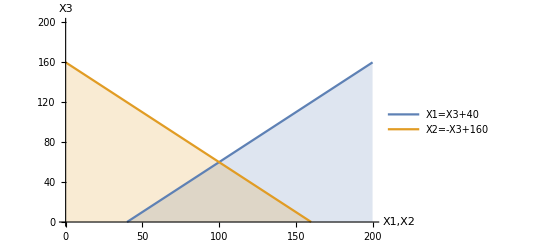

```mathematica
A={{1,0,-1,-1,0},{1,1,0,0,0},{0,1,1,0,-1},{0,0,0,1,1}};
X={x1,x2,x3,x4,x5};
B={40,200,100,60};
MatrixForm[A].MatrixForm[X]==MatrixForm[B]
MatrixForm[augmented = Transpose[Join[Transpose[A], {B}]]]
MatrixForm[rowreduce =RowReduce[augmented]]
MatrixForm[rowreduce [[All,{1,2,3,4,5}]].X==rowreduce [[All,6]]]
Plot[{x-40,-x+160},{x,0,200},PlotRange->{{0,200},{0,200}},AxesLabel->{"X1,X2","X3"},PlotLegends->{"X1=X3+40","X2=-X3+160"},Filling->Axis]
```

{{p[n]→Fibonacci[n]}}

{1,1,2,3,5,8,13,21,34,55,89,144}

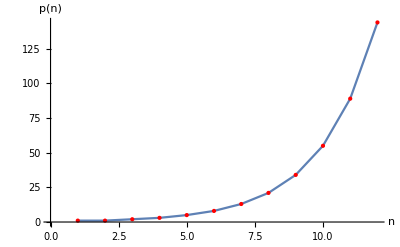

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

{{a→1/(√5),b→-1/(√5)}}

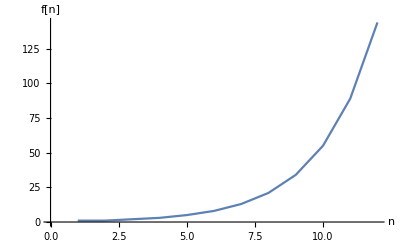

{1.,1.,2.,3.,5.,8.,13.,21.,34.,55.,89.,144.}

1/2 (1+√5)

1.61803

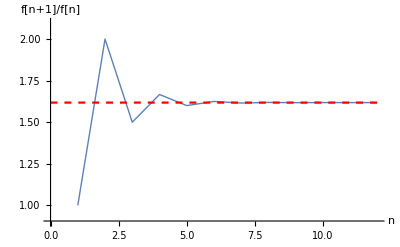

```mathematica
RSolve[{p[n+2]==p[n+1]+p[n],p[1]==p[2]==1},p[n], n]
Table[Fibonacci[n],{n,12}]
ListLinePlot[t=Table[{n,Fibonacci[n]},{n,12}],AxesLabel->{n,p[n]},Epilog->{PointSize[Large],Red,Point[t]}]
Solve[x^2-x-1==0,x]
Solve[a+b==0 &&a*(1+Sqrt[5])/2+b*(1-Sqrt[5])/2==1,{a,b}]
f[n_]:=((1+Sqrt[5])/2)^n/Sqrt[5]-((1-Sqrt[5])/2)^n/Sqrt[5]
ListLinePlot[Table[{n,f[n]},{n,12}],AxesLabel->{n,"f[n]"}]
Table[N[f[n]],{n,12}]
Limit[f[n+1]/f[n],n->Infinity]
N[%]
limitfun=ListLinePlot[Table[{n,f[n+1]/f[n]},{n,12}],AxesLabel->{n,"f[n+1]/f[n]"},PlotRange->{{0,12},{0.9,2.1}},PlotStyle->{Thick}];
limitval=ListLinePlot[Table[{n,1/2 (1+√5)},{n,0,12}],PlotStyle->{Red,Dashed}];
Show[limitfun,limitval]
```